```mathematica
data =Import["C:\\Users\\juhaszn\\Documents\\HAL\\HAL-master\\HAL-master\\StochasticVariability\\theo_results\\theo13.txt", "Table"];
```

dataLength will be 1000, this was just an experiment

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<=dataLength, i++,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
cleanData;
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0}}

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData
```

{{0,376},{1,248},{2,142},{3,105},{4,53},{5,31},{6,19},{7,6},{8,9},{9,7},{10,3},{11,1}}

```mathematica
probDensFunc[x_]:=N[probabilityData[[x+1,2]]/dataLength]
```

```mathematica
probDensFunc[0]
```

0.376

http://math.bme.hu/~nandori/Virtual_lab/stat/expect/Generating.pdf

```mathematica
probGenFunc[z_]:=Sum[probDensFunc[n]*(z^n),{n,0,Max[cleanData]}]
```

```mathematica
probGenFunc[0.01]
```

0.378494

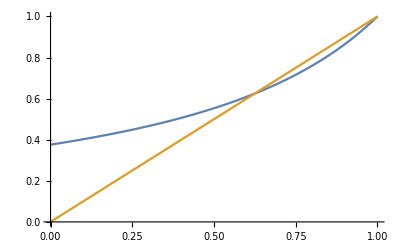

```mathematica
Plot[{probGenFunc[t],t},{t,0,1}]
```